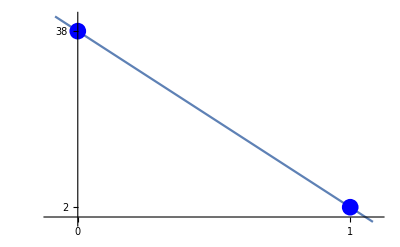

```mathematica
SetOptions[Plot,BaseStyle->{FontSize->16,FontWeight->"Bold"}];
xmin = -.1;
xmax = 1.1;
x0=0;
x1 = 1;
f[x_]:=-36*(x-1)+2;
Plot[f[x],{x,xmin,xmax},Epilog->{PointSize[0.03],Blue,Point[{x0,f[x0]}],PointSize[0.03],Blue,Point[{x1,f[x1]}]},Ticks->{{x0,x1}, {f[x0],f[x1]}},PlotRange->{-1,41}]
```

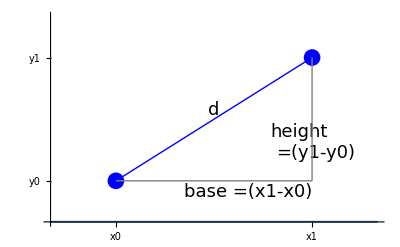

```mathematica
SetOptions[Plot,BaseStyle->{FontSize->16,FontWeight->"Bold"}];
xmin = 0;
xmax = 1.25;
x0=.25;y0=x0;
x1 = 1;y1=x1;
f[x_]:=0;
Plot[f[x],{x,xmin,xmax},Epilog->{Text[Style["d",18],Scaled[{.5,.5}],{0,-1}],Text[Style["base =(x1-x0)",18],Scaled[{.6,.2}],{0,1}],Text[Style["height",18],Scaled[{.75,.4}],{0,-1}],Text[Style["=(y1-y0)",18],Scaled[{.8,.3}],{0,-1}],PointSize[0.03],Blue,Point[{x0,y0}],PointSize[0.03],Blue,Point[{x1,y1}],Blue,Line[{{x0,y0},{x1,y1}}],Gray,Line[{{x0,y0},{x1,y0}}],Line[{{x1,y0},{x1,y1}}]},Ticks->{{{x0,"x0"},{x1,"x1"}}, {{y0,"y0"},{y1,"y1"}}},PlotRange->{0,y1+.25}]
```

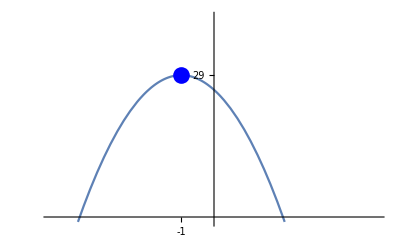

```mathematica
SetOptions[Plot,BaseStyle->{FontSize->16,FontWeight->"Bold"}];
xmin = -5;
xmax = 5;
x0=-1;
f[x_]:=-3*(x+1)^2+29;
Plot[f[x],{x,xmin,xmax},Epilog->{PointSize[0.03],Blue,Point[{x0,f[x0]}]},Ticks->{{x0}, {f[x0]}},PlotRange->{-1,41}]
```

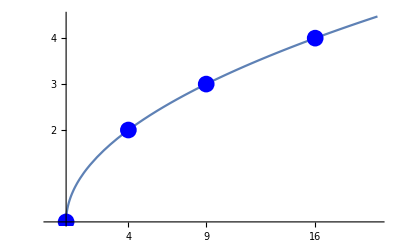

```mathematica
SetOptions[Plot,BaseStyle->{FontSize->16,FontWeight->"Bold"}];
xmin = -1;
xmax = 20;
x0=4;
x1=9;
x2=16;
f[x_]:=Sqrt[x];
Plot[f[x],{x,xmin,xmax},Epilog->{PointSize[0.03],Blue,Point[{0,f[0]}],PointSize[0.03],Blue,Point[{x0,f[x0]}],PointSize[0.03],Blue,Point[{x1,f[x1]}],PointSize[0.03],Blue,Point[{x2,f[x2]}]},Ticks->{{x0,x1,x2}, {f[x0],f[x1],f[x2]}}]
```

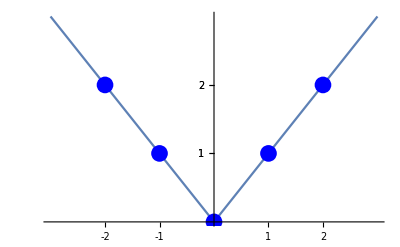

```mathematica
SetOptions[Plot,BaseStyle->{FontSize->16,FontWeight->"Bold"}];
xmin = -3;
xmax = 3;
x0=1;
x1=-1;
x2=2;
x3=-2;
f[x_]:=Abs[x];
Plot[f[x],{x,xmin,xmax},Epilog->{PointSize[0.03],Blue,Point[{0,f[0]}],PointSize[0.03],Blue,Point[{x0,f[x0]}],PointSize[0.03],Blue,Point[{x1,f[x1]}],PointSize[0.03],Blue,Point[{x2,f[x2]}],PointSize[0.03],Blue,Point[{x3,f[x3]}]},Ticks->{{x0,x1,x2,x3}, {f[x0],f[x1],f[x2],f[x3]}}]
```

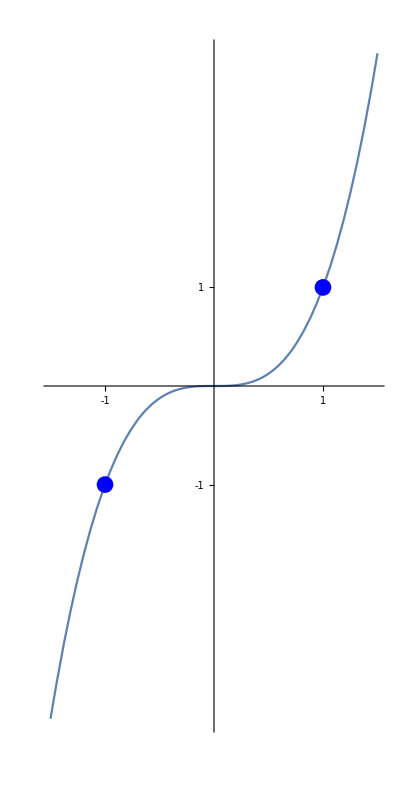

```mathematica
SetOptions[Plot,BaseStyle->{FontSize->16,FontWeight->"Bold"}];
xmin = -1.5;
xmax = 1.5;
x0=1;
x1=-1;
f[x_]:=x^3;
Plot[f[x],{x,xmin,xmax},Epilog->{PointSize[0.03],Blue,Point[{x0,f[x0]}],PointSize[0.03],Blue,Point[{x1,f[x1]}]},Ticks->{{x0,x1}, {f[x0],f[x1]}},Ticks->None,AspectRatio->2]
```

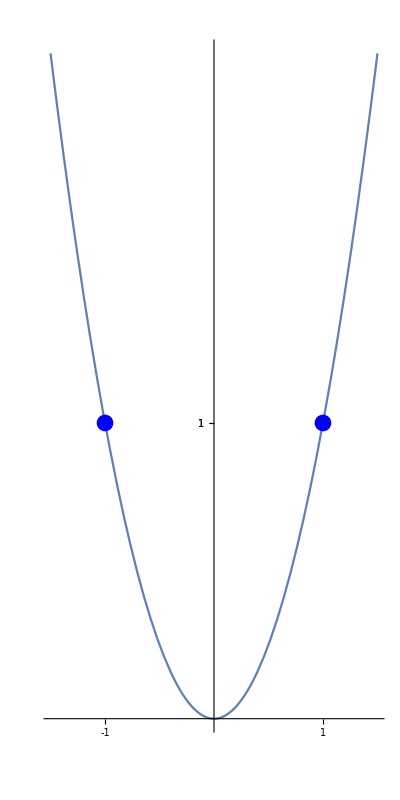

```mathematica
SetOptions[Plot,BaseStyle->{FontSize->16,FontWeight->"Bold"}];
xmin = -1.5;
xmax = 1.5;
x0=1;
x1=-1;
f[x_]:=x^2;
Plot[f[x],{x,xmin,xmax},Epilog->{PointSize[0.03],Blue,Point[{x0,f[x0]}],PointSize[0.03],Blue,Point[{x1,f[x1]}]},Ticks->{{x0,x1}, {f[x0],f[x1]}},Ticks->None,AspectRatio->2]
```

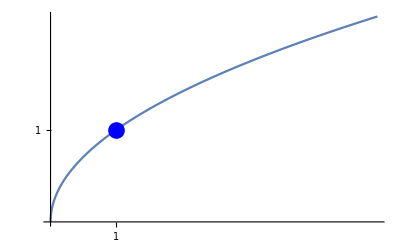

```mathematica
SetOptions[Plot,BaseStyle->{FontSize->16,FontWeight->"Bold"}];
xmin = 0;
xmax = 5;
x0=1;
f[x_]:=x^(1/2);
Plot[f[x],{x,xmin,xmax},Epilog->{PointSize[0.03],Blue,Point[{x0,f[x0]}]},Ticks->{{x0}, {f[x0]}},Ticks->None]
```

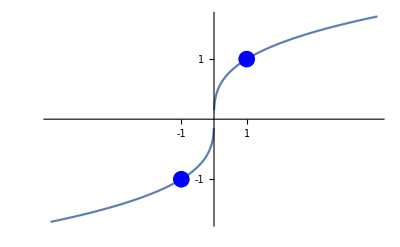

```mathematica
SetOptions[Plot,BaseStyle->{FontSize->16,FontWeight->"Bold"}];
xmin = -5;
xmax = 5;
x0=1;
x1=-1;
f[x_]:=Sign[x]*Abs[x]^(1/3);
Plot[f[x],{x,xmin,xmax},Epilog->{PointSize[0.03],Blue,Point[{x0,f[x0]}],PointSize[0.03],Blue,Point[{x1,f[x1]}]},Ticks->{{x0,x1}, {f[x0],f[x1]}},Ticks->None]
```

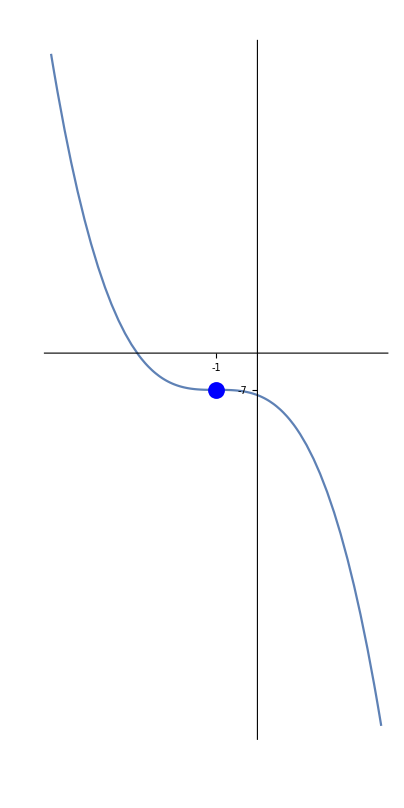

```mathematica
SetOptions[Plot,BaseStyle->{FontSize->16,FontWeight->"Bold"}];
x0=-1;
pm = 4;
xmin = x0-pm;
xmax = x0+pm;
f[x_]:=-(x+1)^3-7;
Plot[f[x],{x,xmin,xmax},Epilog->{PointSize[0.03],Blue,Point[{x0,f[x0]}]},Ticks->{{x0}, {f[x0]}},AspectRatio->2]
```

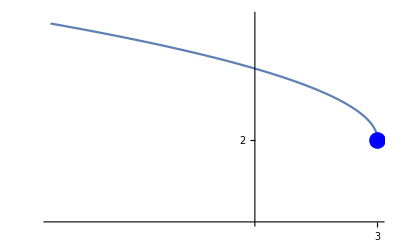

```mathematica
SetOptions[Plot,BaseStyle->{FontSize->16,FontWeight->"Bold"}];
xmin = -5;
xmax = 3;
x0=3;
f[x_]:=(-x+3)^(1/2)+2;
Plot[f[x],{x,xmin,xmax},Epilog->{PointSize[0.03],Blue,Point[{x0,f[x0]}]},Ticks->{{x0}, {f[x0]}},PlotRange->{0,5}]
```

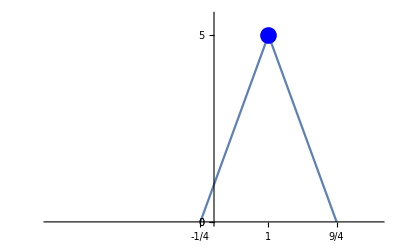

```mathematica
SetOptions[Plot,BaseStyle->{FontSize->16,FontWeight->"Bold"}];
xmin = -3;
xmax = 3;
x0=1;
x1=9/4;
x2=-1/4;
f[x_]:=-4Abs[x-1]+5;
Plot[f[x],{x,xmin,xmax},Epilog->{PointSize[0.03],Blue,Point[{x0,f[x0]}]},Ticks->{{x0,x1,x2}, {f[x0],f[x1],f[x2]}},PlotRange->{0,5.5}]
```

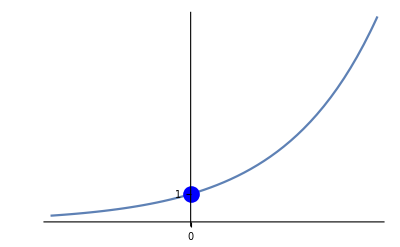

```mathematica
SetOptions[Plot,BaseStyle->{FontSize->16,FontWeight->"Bold"}];
xmin = -1.5;
xmax = 2;
x0=0;
f[x_]:=E^x;
Plot[f[x],{x,xmin,xmax},PlotRange->{0,f[xmax]},Epilog->{PointSize[0.03],Blue,Point[{x0,f[x0]}]},Ticks->{{x0}, {f[x0]}},Ticks->None]
```

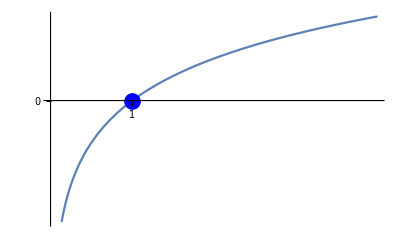

```mathematica
SetOptions[Plot,BaseStyle->{FontSize->16,FontWeight->"Bold"}];
xmin = 0;
xmax = 4;
x0=1;
ymin = -2;
f[x_]:=Log[x];
Plot[f[x],{x,xmin,xmax},PlotRange->{ymin,f[xmax]},Epilog->{PointSize[0.03],Blue,Point[{x0,f[x0]}]},Ticks->{{x0}, {f[x0]}},Ticks->None]
```

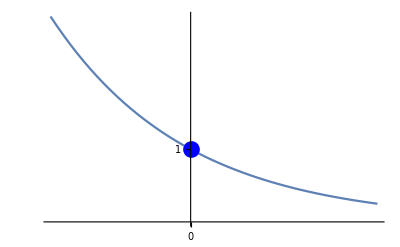

```mathematica
SetOptions[Plot,BaseStyle->{FontSize->16,FontWeight->"Bold"}];
xmin = -1.5;
xmax = 2;
x0=0;
f[x_]:=Abs[(1/2)]^x;
Plot[f[x],{x,xmin,xmax},PlotRange->{0,f[xmin]},Epilog->{PointSize[0.03],Blue,Point[{x0,f[x0]}]},Ticks->{{x0}, {f[x0]}},Ticks->None]
```

General::prng: Value of option PlotRange -> {-2,∞} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

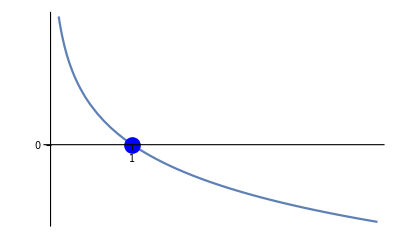

```mathematica
SetOptions[Plot,BaseStyle->{FontSize->16,FontWeight->"Bold"}];
xmin = 0;
xmax = 4;
x0=1;
ymin = -2;
f[x_]:=Log[1/2,x];
Plot[f[x],{x,xmin,xmax},PlotRange->{ymin,f[xmin]},Epilog->{PointSize[0.03],Blue,Point[{x0,f[x0]}]},Ticks->{{x0}, {f[x0]}},Ticks->None]
```